{{T→InterpolatingFunction[…]}}

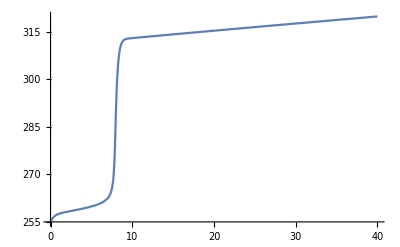

```mathematica
Clear[f,g,h];
ice=0.7;
water =0.2;
meltpoint=273.15;
variance = 20;
f[t_]:=If[t≤0,0,E^(-1/t)];
g[t_]:=f[t]/(f[t]+f[1-t]);
h[t_]:=(water-ice)*g[(t-(meltpoint-variance))/(2*variance)]+ice

S=1367;
α=0.5;
σ=5.670374419*10^(-8);
ϵ=0.612;
a=1;
b=50;
d1[t_] := a*t+b;
d2[t_]:=20*Log[t+1]
Clear[T,t]
s=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d1[t],T[0]==255},T,{t,0,40}]
Plot[Evaluate[T[t]/.s],{t,0,40},PlotRange->All]
```

```mathematica
T=(((1-α)S)/(4*ϵ*σ))^(1/4)
```

264.898